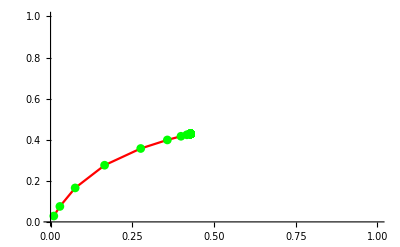

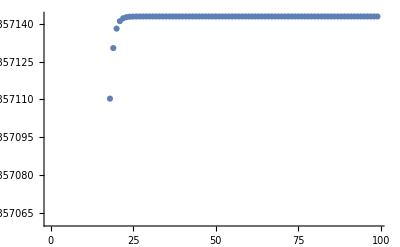

0.428571

```mathematica
naturalSelection[alpha_,beta_,gamma_,n_,p0_]:=(
p=Table[0,n];
p[[1]]=p0;
For[k=1,k<n,k++, p[[k+1]]=((alpha-beta)*p[[k]]*p[[k]]+beta*p[[k]])/((alpha-2*beta+gamma)*p[[k]]*p[[k]]+2*(beta-gamma)*p[[k]]+gamma);
];
p
)
n=100;
alpha=0.1;
beta=0.9;
gamma=0.3;
p0=0.01;
p=naturalSelection[alpha,beta,gamma,n,p0];

linePl=ListLinePlot[Table[{p[[k]],p[[k+1]]},{k,1,n-1}],PlotRangeClipping->False,PlotRange->{{0,1},{0,1}},PlotStyle->Red];
pointPl=ListPlot[Table[{p[[k]],p[[k+1]]},{k,1,n-1}],PlotRangeClipping->False,PlotRange->{{0,1},{0,1}},PlotStyle->Green,PlotMarkers->Automatic];
Show[linePl,pointPl]
ListPlot[Table[{k,p[[k+1]]},{k,1,n-1}]]
N[p[[n]],100]
```